## Data

#### 2 Circles intersection points

```mathematica
point[{x0_,y0_},r1_,{x1_,y1_},r2_]:=Block[{res,c,X=(x1-x0),Y=(y1-y0),ys},
c=(r2^2-r1^2-X^2-Y^2)/-2;
ys=#⟦1,2⟧&/@NSolve[((c-y Y)/X)^2+y^2==r1^2];
res =({(c-# Y)/X,#}+{x0,y0})&/@ys;
Return@res]
```

```mathematica
c1={x1,y1}={-40,0}; r1 =40;
c2 = {x2,y2}={32,0}; r2 = 48;
d=r2-r1;
offset={{0,-.8d},{0,.8d}};
p={p1,p2}=point[c1,r1,c2,r2]+offset;
```

## Calculations

#### Tangent to the circumference throuhg the point

```mathematica
func[{a_,b_},{cx_,cy_},r_]:=Block[{x2,x1,x0,ks,bs,res},
x2=k^2+1;
x1=2k b - 2k cy -2 k^2 a -2 cx;
x0=cx^2+cy^2+a^2 k^2+b^2-r^2-2b cy -2k b a +2k a cy;
ks=NSolve[x1^2-4x0 x2==0,k];
res={#⟦1,2⟧,b-#⟦1,2⟧a}&/@ks;
Return@res]
```

#### Intersection point of a line and a circle

```mathematica
inter[{k_,b_},{cx_,cy_},r_]:=Block[{res},
res={#⟦1,2⟧,#⟦2,2⟧}&/@NSolve[{y==k x + b, (x-cx)^2+(y-cy)^2==r^2},{x,y}];
Return@Re[res];
]
```

#### Return list of intersection points of

```mathematica
final[c1_,r1_,c2_,r2_,p_]:=Block[{res,ps},
ps={inter[#,c1,r1]&/@func[p,c1,r1],inter[#,c2,r2]&/@func[p,c2,r2]}//Flatten[#,2]&//DeleteDuplicates;
res= Sort[ps,#1⟦2⟧>#2⟦2⟧&];
Return@res]
```

```mathematica
{l11,l12}=func[p2,c1,r1]
{l21,l22}=func[p2,c2,r2]
```

{{-2.75773,7.02844},{-0.347146,28.4558}}

{{0.593996,36.8215},{3.4867,62.5344}}

```mathematica
{i11,i12}=inter[l12,c1,r1]
{i21,i22}=inter[l21,c2,r2]
```

{{-26.8821,37.7878},{-26.8821,37.7878}}

{{7.48663,41.2686},{7.48663,41.2686}}

```mathematica
final[c1,r1,c2,r2,p2]
```

{{7.48663,41.2686},{-26.8821,37.7878},{-2.39597,13.6359},{-14.1398,13.2331}}

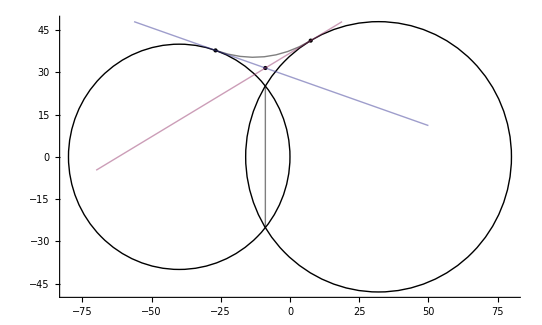

```mathematica
Show[{
Graphics[{
Circle[c1,r1],
Circle[c2,r2],

PointSize[Medium],
Point[{p2,i11,i22}],

Opacity[0.5],
Line[point[c1,r1,c2,r2]],

BezierCurve[{i11,p2,i22}]
}],
Plot[{
l12.{x,1}==0,
l21.{x,1}==0
},{x,-70,50},PlotRange->{{-60,60},{-48,48}},PlotStyle->Opacity[0.5]]
},Axes->True]
```

## Test

```mathematica
val1[t_]:=If[Sign[t]<0,Abs@t,0]
val2[t_]:=If[Sign[t]>0,Abs@t,0]
```

```mathematica
Manipulate[
Module[{cp1,R1,cp2,R2,mid1,mid2, curve1,curve2},
cp1={-Abs@t*4d-d*val1@t,0};
cp2={Abs@t*4d+d*val2@t,0};
R1 = r2-d*val1@t;
R2=r2-d*val2@t;
{mid1,mid2}=point[cp1,R1,cp2,R2]+{{0,-.8d * Abs@t},{0,.8d * Abs@t}};
curve1 = Insert[final[cp1,R1,cp2,R2,mid2]⟦1;;2⟧,mid2,2];
curve2 = Insert[final[cp1,R1,cp2,R2,mid1]⟦3;;4⟧,mid1,2];
Show[{
Graphics[{
Circle[cp1,R1],
Circle[cp2,R2],
(*PointSize[Medium],
Point[{mid1,mid2,cp1,cp2}],*)
BezierCurve[curve1],
BezierCurve[curve2]
}]},Axes->False,PlotRange->{{-82,82},{-65,65}},ImageSize->350]
],{t,-1.05,1.05}]
```

```mathematica
Animate[
Module[
{cp1,R1,cp2,R2,mid1,mid2, curve1,curve2},
cp1={-Abs@t*4d-d*val1@t,0};
cp2={Abs@t*4d+d*val2@t,0};
{R1,R2} = {r2-d*val1@t,r2-d*val2@t};
{mid1,mid2}=point[cp1,R1,cp2,R2]+{{0,-.8d * Abs@t},{0,.8d * Abs@t}};
curve1 = Insert[final[cp1,R1,cp2,R2,mid2]⟦1;;2⟧,mid2,2];
curve2 = Insert[final[cp1,R1,cp2,R2,mid1]⟦3;;4⟧,mid1,2];
Show[{
Graphics[{
Circle[cp1,R1],
Circle[cp2,R2],
(*PointSize[Medium],
Point[{mid1,mid2,cp1,cp2}],*)
BezierCurve[curve1],
BezierCurve[curve2]
}]},Axes->False,PlotRange->{{-82,82},{-65,65}},ImageSize->350]
],
{t,-1.05,1.05},
AnimationRunning->False,
AnimationDirection->ForwardBackward, 
AnimationRate->1.5]
```